## (* Essay text inspired by THIS, decided to use the AdministrativeDivision in order to check some theories What is the relation between uninsured people, gini index and death rates along the US states? blah blah blah, no significant correlation. What if we want to see entities that have the biggest impact on death rates on US states? Go big or go home (* Introductions *)

```mathematica
EntityProperties["AdministrativeDivision"];
```

```mathematica
usstates=EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]];
```

```mathematica
GeoRegionValuePlot[usstates->category2,ColorFunctionScaling->True]
```

```mathematica
(* 
annual births-deaths-population - health insurance - "civilian unemployment rate", employment - "uninsured population fraction" "people with/out health insurance "home ownership rate""   "home vacancy rate"
"infant deaths" "minimum wage" "per capita income" "population by poverty status" "population density" "position"
*)
```

```mathematica
(* annual deaths / population = % of people per state who die every year *)
```

```mathematica
(* people without health insurance / population = % of people who do not have health insurance *)
```

```mathematica
(* other stuff that may be interesting from the above list *)
```

## (* Preliminary for CE: *)

```mathematica
data=Dataset[<|"states"->usstates,"noHI"->QuantityMagnitude@ EntityValue[usstates,EntityProperty["AdministrativeDivision","HealthInsuranceUncoveredRate"]],"deaths"->QuantityMagnitude@(EntityValue[usstates,EntityProperty["AdministrativeDivision","AnnualDeaths"]]/EntityValue[usstates,EntityProperty["AdministrativeDivision","Population"]])*100,"gini"->QuantityMagnitude@ EntityValue[usstates,EntityProperty["AdministrativeDivision","GiniIndex"]]|>];
```

```mathematica
data
```

Dataset[<>]

## (* Working on the US *)

```mathematica
(*dataus may not be needed*)
```

```mathematica
fithideath = Fit[Transpose@{Normal@data["noHI"],Normal@data["deaths"]},{1,x},x]
```

0.886338+0.000206964 x

```mathematica
fitdeathgini =Fit[Transpose@{Normal@data["gini"],Normal@data["deaths"]},{1,x},x]
```

0.281994+1.30913 x

```mathematica
fithigini = Fit[Transpose@{Normal@data["gini"],Normal@data["noHI"]},{1,x},x]
```

-8.28973+48.5082 x

```mathematica
Keys[data]
```

Dataset[<>]

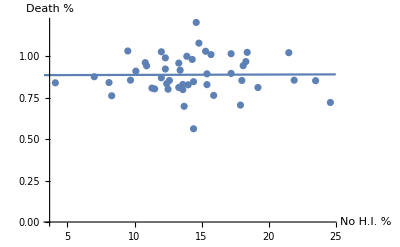

```mathematica
Show[ListPlot[Transpose@{Normal@data["noHI"],Normal@data["deaths"]},PlotRange->All],Plot[fithideath,{x,0,25}],AxesLabel->{"No H.I. %","Death %"}]
```

```mathematica
Correlation[Normal@data["noHI"],Normal@data["deaths"]]
```

0.00736841

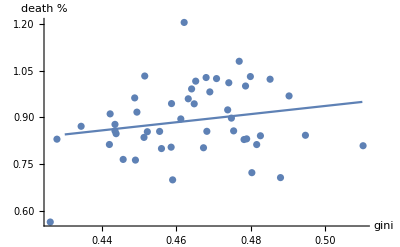

```mathematica
Show[ListPlot[Transpose@{Normal@data["gini"],Normal@data["deaths"]},PlotRange->Full],Plot[fitdeathgini,{x,0.43,0.51}],PlotRange-> All  , AxesLabel->{"gini","death %"}]
```

```mathematica
Correlation[Normal@data["gini"],Normal@data["deaths"]]
```

0.202066

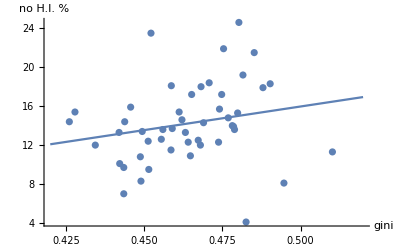

```mathematica
Show[ListPlot[Transpose[{Normal[data["gini"]],Normal[data["noHI"]]}],PlotRange->Full],Plot[fithigini,{x,0.42,0.52}],PlotRange->All,AxesLabel->{"gini","no H.I. %"}]
```

```mathematica
Correlation[Normal@data["gini"],Normal@data["noHI"]]
```

0.210305

```mathematica
(* Choose some other quantities, create correlation plots *)
```

```mathematica
(* Test ALL the features. Show the ones with the largest correlation *)
```

```mathematica
(* Will have to normalise some to population etc etc *)
```

```mathematica
(* New Round *)
```

```mathematica
(*allentities = EntityProperties["AdministrativeDivision"][[;;6]] *)
```

```mathematica
(* The go big or go home part *)
```

```mathematica
(* Some good stuff happen here *)
```

```mathematica
rateentities=Complement[ Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "Fraction"] ||StringContainsQ[CanonicalName[#], "Rate"]||StringContainsQ[CanonicalName[#], "Economic"]|| StringContainsQ[CanonicalName[#], "Gini"]||StringContainsQ[CommonName[#], "per capita"]||StringContainsQ[CanonicalName[#], "Density"]||StringContainsQ[CanonicalName[#], "Median"]||StringContainsQ[CanonicalName[#], "Average"]&],{EntityProperty["AdministrativeDivision","BusinessEthnicOwnershipFractions"],EntityProperty["AdministrativeDivision","BusinessGenderOwnershipFractions"],EntityProperty["AdministrativeDivision","CountySalesTaxRate"]}];
```

```mathematica
rateentities
```

{rate of aggravated assault,housing units change rate,average ACT composite score,average ACT English score,average ACT math score,average ACT reading score,average ACT science score,average commute time,average home sale price,average SAT reading score,average SAT math score,average SAT writing score,average total SAT score,rate of burglary,Amerindian business ownership fraction,Asian business ownership fraction,black business ownership fraction,Hispanic business ownership fraction,Pacific Islander business ownership fraction,white business ownership fraction,civilian unemployment rate,coincident economic activity index,total rate of crime,average earnings per job,federal government expenditure per capita,rate of rape,fraction foreign born,high school graduates taking ACT,high school graduates taking SAT,Gini index,insured population fraction,uninsured population fraction,highest sales tax rate,home ownership rate,home vacancy rate,housing in multiple unit structures,rate of larceny,lowest sales tax rate,median age,median household income,median home sale price,median total sales tax rate,rate of motor vehicle thefts,rate of murder and nonnegligent manslaughter,median owner-occupied home value,owner-occupied housing,per capita income,per capita personal income,population density,total rate of property crime,residential rental vacancy rate,retail sales per capita,rate of robbery,state sales tax rate,total voter registration rate,total voting rate,total rate of violent crime}

```mathematica
Length@rateentities
```

57

```mathematica
numbersentities=Complement[Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CommonName[#], "number"]||StringContainsQ[CommonName[#], "people"]||StringContainsQ[CommonName[#], "annual"]&],{EntityProperty["AdministrativeDivision","PersonsPerHousehold"]}];
```

```mathematica
Length@numbersentities
```

15

```mathematica
numbersentities
```

{number of aggravated assaults,annual births,annual deaths,number of burglaries,number of businesses,total number of crimes,disabled people,number of rapes,people with health insurance,people without health insurance,number of larcenies,number of motor vehicle thefts,total number of property crimes,number of robberies,total number of violent crimes}

```mathematica
(* Normalise by population here, if needed *)
```

```mathematica
(*Important starts here*)
```

```mathematica
(* Make the list of most correlated values, remove the ones that share key words, check the resulting correlations *)
```

```mathematica
(* Maybe play with the units of meassurement, to decide you quantities need normalisation *)
```

```mathematica
ratesvalues= EntityValue[usstates,rateentities]//QuantityMagnitude;
```

```mathematica
numbersvalues =(EntityValue[usstates,numbersentities]//QuantityMagnitude)/(EntityValue[usstates,"Population"]//QuantityMagnitude);
```

```mathematica
allentities=Join[rateentities,numbersentities];
```

```mathematica
allentities//Dimensions
```

{72}

```mathematica
numbersvalues//Dimensions
```

{48,15}

```mathematica
values=Join[ratesvalues,numbersvalues,2];
```

```mathematica
values[[All,5]]//Length
```

48

```mathematica
values//Dimensions
```

{48,72}

```mathematica
result=Table[{usstates[[i]],allentities[[j]],values[[i,j]]},{i,Length[usstates]},{j,Length[allentities]}];
```

```mathematica
result//Dimensions
```

{48,72,3}

```mathematica
(*correlations=Table[{rateentities[[i]],rateentities[[j]],Correlation[result[[All,i,3]],result[[All,j,3]]]},{i,Length[rateentities]},{j,i-1}];*)
```

```mathematica
(*correlationlist=Flatten[correlations,1]//SortBy[Abs[#[[3]]]&]//Reverse//N;*)
```

#### (* Only uninsured starts here *)

```mathematica
(* Make the list of most correlated values, remove the ones that share key words, check the resulting correlations *)
```

```mathematica
(* Maybe play with the units of meassurement, to decide you quantities need normalisation *)
```

```mathematica
uninsurancedvalues =EntityValue[usstates,EntityProperty["AdministrativeDivision","HealthInsuranceUncoveredRate"]]//QuantityMagnitude;
```

```mathematica
deathsvalues=QuantityMagnitude@(EntityValue[usstates,EntityProperty["AdministrativeDivision","AnnualDeaths"]]/EntityValue[usstates,EntityProperty["AdministrativeDivision","Population"]])*100//N;
```

```mathematica
correlations=Table[{allentities[[i]],EntityProperty["AdministrativeDivision","AnnualDeaths"],Correlation[result[[All,i,3]],deathsvalues]},{i,Length[allentities]}];
```

```mathematica
correlations//Dimensions
```

{72,3}

```mathematica
correlationlist=SortBy[Abs[#[[3]]]&]@correlations//Reverse//N;
```

```mathematica
correlationlist//Dimensions
```

{72,3}

```mathematica
correlationlist[[;;20]]//Column
```

{annual deaths,annual deaths,1.}
{disabled people,annual deaths,0.820064}
{median household income,annual deaths,-0.610501}
{median age,annual deaths,0.607429}
{coincident economic activity index,annual deaths,-0.559576}
{median owner-occupied home value,annual deaths,-0.490113}
{annual births,annual deaths,-0.483335}
{fraction foreign born,annual deaths,-0.459052}
{per capita personal income,annual deaths,-0.4419}
{median home sale price,annual deaths,-0.436554}
{average home sale price,annual deaths,-0.433844}
{per capita income,annual deaths,-0.424941}
{Pacific Islander business ownership fraction,annual deaths,-0.39552}
{rate of murder and nonnegligent manslaughter,annual deaths,0.393345}
{home ownership rate,annual deaths,0.390882}
{home vacancy rate,annual deaths,0.385098}
{Asian business ownership fraction,annual deaths,-0.374575}
{housing in multiple unit structures,annual deaths,-0.370476}
{owner-occupied housing,annual deaths,0.361417}
{average earnings per job,annual deaths,-0.338782}